# Github Test

## Source: https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/Misc/GitHubDataObjects.m

## Code

```mathematica
(*GitHubDataObjects Mathematica package Copyright (C) 2015 Anton Antonov This program is free software:you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation,either version 3 of the License,or (at your option) any later version.This program is distributed in the hope that it will be useful,but WITHOUT ANY WARRANTY;without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.See the GNU General Public License for more details.You should have received a copy of the GNU General Public License along with this program.If not,see<http://www.gnu.org/licenses/>.Written by Anton Antonov,antononcube@gmail.com,Windermere,Florida,USA.*)(*Mathematica is (C) Copyright 1988-2015 Wolfram Research,Inc.Protected by copyright law and international treaties.Unauthorized reproduction or distribution subject to severe civil and criminal penalties.Mathematica is a registered trademark of Wolfram Research,Inc.*)(* :Title:GitHubDataObjects*)(* :Author:Anton Antonov*)(* :Date:2015-10-15*)(* :Package Version:0.1*)(* :Mathematica Version:10.2*)(* :Copyright:(c) 2015 Anton Antonov*)(* :Keywords:GitHub,commit,plot,design patterns,Template Method,Strategy,Decorator,Composite,GoF*)(* :Discussion:This package provides object-oriented implementation of visualization and query tasks of commits data from GiHub.The implementation uses the design patterns Template Method,Strategy,Decorator,and Composite described in the book:[GoF-94] Erich Gamma,Richard Helm,Ralph Johnson,John Vlissides,Design Patterns:Elements of Reusable Object-Oriented Software,Addison-Wesley,1994. The implementation is a modified and extended version of the functions in the package "GitHubPlots.m".(Which is also provided in this MathematicaForPrediction GitHub project.) The most significant feature of this package is the method "Plot3D" for a collection of GitHub projects.Here is an example how to use it:ghs=Map[MakeGitHubDataObject["hadley",#]&,{"plyr","dplyr","adv-r","ggplot2","devtools","rvest"}] ghComposite=GitHubDataComposite[Unique[],ghs] Through[ghComposite["GetChildren"[]]@"Project"[]] ghComposite["Plot3D"["ProjectPlanes"->True,BoxRatios->{1,2,2}]] ghComposite["Plot3D"["ProjectPlanes"->False,"GlobalTimeOrder"->False,"SubsetQueryFunction"->(StringMatchQ[#committer,___~~"Hadley"|"hadley"~~___]&),"SubsetLines"->True,"SubsetPlotStyle"->{PointSize[0.02],Lighter[Purple],Arrowheads[10^-7.7,Appearance->"Flat"]},PlotLabel->"Hadley Wickham",BoxRatios->{1,2,2}]] Descriptions of the options follow.1. "ProjectPlanes"->True|False Should planes for the projects be drawn on the 3D plot.2. "GlobalTimeOrder"->True|False Should the points be ordered globally in time or for each project separately.If False the points of each project are given Z coordinate corresponding to their commit order.If True the points of all projects are ordered according to their times and their Z coordinates are derived from that global order.3. "SubsetQueryFunction"->selectFunc Allows for selection of points that adhere to a predicate.The function selectFunc is used in the Dataset's corresponding to the projects and from the obtained rows the subset of points is derived.4. "SubsetLines"->True|False Should line segments (arrows) be drawn between the subset points.5. "SubsetPlotStyle"->subPloStyle Graphics3D directive for the color,size,etc.of the points and lines corresponding to the specified subset.6. Other Graphics3D options passed to Graphics3D.The implementation description with design patterns:-Template Method is used for the general flow of the data obtaining,parsing,and plotting.-Strategy is used for the different types of plots based on DateListPlot,BarChart,and Graphics3D.-Decorator is used to endow the DateListPlot based plots with lines of the commit dependencies.-Decorator is used to give color to the ticks and points in the plots.-For a collection of GitHub projects Composite is used to obtain plots with uniform ranges,and to make a 3D plot of the data of all projects highlighting a subset of the data points.The functions are not put into a real Mathematica package because the implementations were made for didactic purposes.TODO:1. Implement standard functions based on the classes/objects implemented here.2. Refactor the code to be able to work with other types time logs data.This file was created using Mathematica Plugin for IntelliJ IDEA.Anton Antonov 2015-10-15*)(**********************************************************)(*Creation*)(**********************************************************)(*Clear[GitHubData]*)MakeGitHubDataObject[user_String,project_String]:=Block[{objID=Unique[]},GitHubData[{objID,user,project}];
GitHubData[{objID,user,project}]["CommitData"]={};
GitHubData[{objID,user,project}]["PlotFunction"]=GHDDateListPlot;
GitHubData[{objID,user,project}]];

(**********************************************************)
(*Data download*)
(**********************************************************)

GitHubData[args__]["GetData"[]]:=GitHubData[args]["GetData"[1,30]];

GitHubData[{objID_,user_String,project_String}]["GetData"[page_Integer,perPage_Integer]]:=Block[{obj=GitHubData[{objID,user,project}],url,data},If[Length[obj["CommitData"]]==0,url=StringTemplate["https://api.github.com/repos/`1`/`2`/commits?page=`3`&per_page=`4`"];
data=Import[url[user,project,ToString[page],ToString[perPage]],"JSON"];
obj["CommitData"]=data;];
obj["CommitData"]];


(**********************************************************)
(*Parsing*)
(**********************************************************)

Clear[ParseGitRecord]
ParseGitRecord[recRules_]:=Block[{sha,message,committer,date,parentSha,htmlURL},(*Print["ParseGitRecord called."];*)sha="sha"/. recRules;
message=StringReplace["message"/. ("commit"/. recRules),Whitespace->" "];
committer="name"/. ("committer"/. ("commit"/. recRules));
date="date"/. ("committer"/. ("commit"/. recRules));
parentSha="sha"/. ("parents"/. recRules);
htmlURL="html_url"/. recRules;
Thread[{"sha","message","committer","date","parentSha","htmlURL"}->{sha,message,committer,date,parentSha,htmlURL}]];


GitHubData[{objID_,user_String,project_String}]["ParseData"[]]:=Block[{obj=GitHubData[{objID,user,project}],commitRecs,graphRules,unknown,unknownDate},(*Similarly to the previous implementation code.*)If[Length[obj["CommitRecords"]]==0||!ListQ[obj["CommitRecords"]],Evaluate[obj]["CommitRecords"]=SortBy[ParseGitRecord/@obj["GetData"[]],"date"/. #&];
(*A shortcut.*)commitRecs=GitHubData[{objID,user,project}]["CommitRecords"];
(*Make a commits graph rules*)graphRules=Flatten@Map[Thread,("parentSha"->"sha")/. commitRecs];
(*Find the unknown parents and add empty records for them.*)unknown=Complement[Union[Flatten[List@@@graphRules]],"sha"/. commitRecs];
(*Offset the commit dates of the unknown commits to be one day behind.*)unknownDate=DateString[Min[Map[AbsoluteTime[DateList[#]]&,"date"/. commitRecs]]-24*3600];
(*Add records for the unknown commits.*)commitRecs=Join[commitRecs,Map[{"sha"->#,"message"->"none","committer"->"unknown","date"->unknownDate,"parentSha"->"none"}&,unknown]];
commitRecs=SortBy[commitRecs,DateList["date"/. #]&];
(*Assign and return result.*)obj["CommitRecords"]=commitRecs;];
obj["CommitRecords"]];

(**********************************************************)
(*Template Method for "Plot"*)
(**********************************************************)
GitHubDataHEAD=GitHubData;

GitHubData[{objID_,user_String,project_String}]["TickLabels"[]]:=Block[{obj=GitHubDataHEAD[{objID,user,project}],commitRecs,tickLabels},commitRecs=obj["ParseData"[]];
tickLabels={"message",Style["committer",GrayLevel[0.7]],Style["date",GrayLevel[0.8]]}/. commitRecs;
tickLabels[[All,1]]=StringReplace[#,WhitespaceCharacter->" "]&/@tickLabels[[All,1]];
tickLabels];


GitHubData[{objID_,user_String,project_String}]["DatePoints"[]]:=Block[{obj=GitHubDataHEAD[{objID,user,project}],commitRecs},commitRecs=obj["ParseData"[]];
MapThread[{AbsoluteTime[DateList[#1]],#2}&,{"date"/. commitRecs,Range[Length[commitRecs]]}]];


GitHubData[{objID_,user_String,project_String}]["Plot"[opts___]]:=Block[{obj=GitHubDataHEAD[{objID,user,project}],commitRecs,tickLabels,datePoints},commitRecs=obj["ParseData"[]];
tickLabels=obj["TickLabels"[]];
datePoints=obj["DatePoints"[]];
obj["PlotFunction"][datePoints,tickLabels,opts]];


(**********************************************************)
(*Plot strategies*)
(**********************************************************)

GHDDateListPlot[datePoints_,tickLabels_,opts:OptionsPattern[]]:=DateListPlot[MapThread[Tooltip[#1,#2]&,{datePoints,tickLabels}],opts,Joined->False,PlotStyle->{PointSize[0.03]},PlotRange->All,AspectRatio->2,ImageSize->{Automatic,800},GridLines->{None,Automatic},FrameTicks->{{Automatic,Table[{i,Style[tickLabels[[i]],FontSize->14]},{i,1,Length[tickLabels]}]},{Automatic,Automatic}},FrameLabel->{{"commit order",None},{1,1} "date"}];

GHDBarChart[datePoints_,tickLabels_,opts:OptionsPattern[]]:=Block[{distancesFromNow=Map[DateDifference[DateList[#],Date[]]&,datePoints[[All,1]]]},BarChart[distancesFromNow,opts,BarOrigin->Right,BarSpacing->0.5,ChartElementFunction->"GradientScaleRectangle",Frame->True,GridLines->Automatic,Method->{"GridLinesInFront"->True},PlotRangePadding->{{None,0.5},{None,0.3}},FrameLabel->{{"commit order",None},{1,1} "number of days"},FrameTicks->{{Automatic,Table[{i,Style[tickLabels[[i]],FontSize->14]},{i,1,Length[tickLabels]}]},{Automatic,Automatic}},AspectRatio->3,ImageSize->{Automatic,700}]];

GHDGraphics3D[datePoints_,tickLabels_,opts:OptionsPattern[]]:=Block[{distancesFromNow=Map[DateDifference[DateList[#],Date[]]&,datePoints[[All,1]]],committers=Union[tickLabels[[All,2]]],committersAssoc},committersAssoc=AssociationThread[committers,Range[Length[committers]]];
Graphics3D[{Pink,PointSize[0.03],Point[MapThread[{#1,committersAssoc[#2],#3}&,{distancesFromNow[[All,1]],tickLabels[[All,2]],datePoints[[All,2]]}]],GrayLevel[0.5],Line[MapThread[{#1,committersAssoc[#2],#3}&,{distancesFromNow[[All,1]],tickLabels[[All,2]],datePoints[[All,2]]}]]},opts,BoxRatios->{1,1,4},FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},Axes->True,AxesLabel->{"number of days ago","committer","commit order"},Ticks->{Automatic,Table[{i,committers[[i]]},{i,1,Length[committers]}],Table[{i,Style[tickLabels[[i,1]],FontSize->14]},{i,1,Length[tickLabels]}]}]];


(**********************************************************)
(*Other methods*)
(**********************************************************)

GitHubData[{objID_,user_String,project_String}]["Dataset"[]]:=Dataset[Association/@GitHubData[{objID,user,project}]["CommitRecords"]];

GitHubData[{objID_,user_String,project_String}]["DatasetExtended"[]]:=Block[{datePoints,extendedRules},datePoints=GitHubData[{objID,user,project}]["DatePoints"[]];
extendedRules=Thread[{GitHubData[{objID,user,project}]["ParseData"[]],Thread["datePoint"->datePoints],"project"->project}];
Dataset[Association/@extendedRules]];

GitHubData[{objID_,user_String,project_String}]["ReferenceGraph"[]]:=Block[{graphRules,commitsGraph},graphRules=Flatten@Map[Thread,("parentSha"->"sha")/.
GitHubData[{objID,user,project}]["ParseData"[]]];
commitsGraph=Graph[DirectedEdge@@@graphRules];
commitsGraph];

GitHubData[{objID_,user_String,project_String}]["User"[]]:=user;

GitHubData[{objID_,user_String,project_String}]["Project"[]]:=project;

(**********************************************************)
(*GitHubDataDecorators*)
(**********************************************************)

Clear[GitHubDataComponent,GitHubDataDecorator,GitHubDataColorFunctionDecorator]

GitHubDataComponentHEAD=GitHubDataComponent;
GitHubDataComponent[{objID_,user_String,project_String}]["Plot"[opts___]]:=Print["Error"];

GitHubDataDecorator[{objID_,user_String,project_String},component_][s_]:=Block[{GitHubDataComponentHEAD=GitHubDataDecorator},(*Print["Decorator abstract component call. Head[component]=",Head[component]];*)(*Use GitHubDataComponent[{objID,user,project},component][s] in the concrete decorators.*)component[s]];
GitHubDataDecorator[{objID_,user_String,project_String},component_]["Plot"[opts___]]:=component["Plot"[opts]];

GitHubDataColorFunctionDecorator[{objID_,user_String,project_String},component_][s_]:=Block[{GitHubDataComponentHEAD=GitHubDataColorFunctionDecorator},GitHubDataDecorator[{objID,user,project},component][s]];

GitHubDataColorFunctionDecorator[{objID_,user_String,project_String},component_]["Plot"[opts___]]:=Block[{obj=GitHubDataDecorator[{objID,user,project},component],gr,commitRecs,datePoints,colorFunc,pSize},gr=obj["Plot"[DeleteCases[{opts},(PointSize->_)|("DecoratorColorFunction"->_)]]];
(*get option values*)colorFunc=OptionValue[Join[{opts},{"DecoratorColorFunction"->(Blend[{Black,Red},#]&)}],"DecoratorColorFunction"];
pSize=OptionValue[Join[{opts},{PointSize->0.015}],PointSize];
(*decorate the tick labels*)gr=gr/. {GrayLevel[x_]:>colorFunc[x]};
(*decorate the graphics*)If[obj["PlotFunction"]===GHDDateListPlot,commitRecs=obj["ParseData"[]];
datePoints=obj["DatePoints"[]];
gr=Show[{gr,Graphics[{colorFunc[0.2],Line[datePoints],colorFunc[1],PointSize[pSize],Point[datePoints]}]}]];
gr];


(**********************************************************)
(*GitHubDataMessageHyperlinks*)
(**********************************************************)

GitHubDataMessageHyperlinks[{objID_,user_String,project_String}][s_]:=Block[{GitHubDataHEAD=GitHubDataMessageHyperlinks},GitHubData[{objID,user,project}][s]];

GitHubDataMessageHyperlinks[{objID_,user_String,project_String}]["TickLabels"[]]:=Block[{tickLabels},tickLabels=GitHubData[{objID,user,project}]["TickLabels"[]];
tickLabels[[All,1]]=MapThread[Function[{mess,url},Button[Mouseover[Style[mess,"Text"],Style[mess,"HyperlinkActive"]],NotebookLocate[{URL[url],None}],Appearance->None]],{tickLabels[[All,1]],"htmlURL"/. commitRecs}];
tickLabels];


(**********************************************************)
(*GitHubDataCommitPathsDecorator*)
(**********************************************************)

GitHubDataCommitPathsDecorator[{objID_,user_String,project_String},component_][s_]:=Block[{GitHubDataComponentHEAD=GitHubDataCommitPathsDecorator},GitHubDataDecorator[{objID,user,project},component][s]];

GitHubDataCommitPathsDecorator[{objID_,user_String,project_String},component_]["Plot"[opts___]]:=Block[{obj=GitHubDataDecorator[{objID,user,project},component],gr,commitRecs,graphRules,commitsGraph,roots,leaves,paths,shaInds,pathsByInds,datePoints,pointSize=0.03},(*Base plot*)gr=obj["Plot"[opts]];
(*If the right function is used decorate it*)If[obj["PlotFunction"]===GHDDateListPlot,(*Make a commits graph*)commitRecs=obj["ParseData"[]];
graphRules=Flatten@Map[Thread,("parentSha"->"sha")/. commitRecs];
commitsGraph=Graph[DirectedEdge@@@graphRules];
(*Find paths*)roots=Select[graphRules,#[[1]]=="none"&][[All,2]];
leaves=Complement[graphRules[[All,2]],graphRules[[All,1]]];
paths=Flatten[Outer[FindPath[commitsGraph,#1,#2,Length[commitRecs],All]&,roots,leaves],2];
paths=SortBy[paths,-Length[#]&];
shaInds=AssociationThread["sha"/. commitRecs,Range[Length[commitRecs]]];
pathsByInds=Map[shaInds/@#&,paths];
(*Combine the base plot and with the paths plot*)datePoints=obj["DatePoints"[]];
gr=Show[gr,Graphics[{Opacity[0.5],Thickness[0.01],MapThread[{ColorData["TemperatureMap"][#2],Mouseover[Line[datePoints[[#1]]],{Red,PointSize[pointSize*1.18],Point[datePoints[[#1]]]}]}&,{pathsByInds,RandomSample[Range[0,1,1/(Length[pathsByInds]-1)]]}],Opacity[1],LightBlue,PointSize[pointSize*0.66],MapThread[Tooltip[Point[#1],Row[{#2," ",DateDifference[#1[[1]],Date[],{"Month","Day","Hour","Minute"}]," ago"}]]&,{datePoints,"sha"/. commitRecs}]}]]];
gr];


(**********************************************************)
(*GitHubDataComposite*)
(**********************************************************)
ClearAll[GitHubDataCompositeComponent,GitHubDataComposite]

(*The Component*)
GitHubDataCompositeComponentHEAD=GitHubDataCompositeComponent;

GitHubDataCompositeComponent[objID_,children_]["AddChild"[newChild_]]:=GitHubDataCompositeHEAD[objID,Append[children,newChild]];

GitHubDataCompositeComponent[objID_,children_]["GetChild"[childIndex_]]:=children[[childIndex]];

GitHubDataCompositeComponent[objID_,children_]["GetChildren"[]]:=children;

(*GitHubDataCompositeComponent[objID_,children_]["Plot"[___]]:=*)
(*Print["Error: GitHubDataCompositeComponent is an abstract class."];*)

GitHubDataCompositeComponent[objID_,children_][s_]:=Print["Error: GitHubDataCompositeComponent is an abstract class."];

(*The Composite*)
GitHubDataComposite[objID_,children_]["AddChild"[newChild_]]:=Block[{GitHubDataCompositeComponentHEAD=GitHubDataComposite},GitHubDataCompositeComponent[objID,children]["AddChild"[newChild]]];

GitHubDataComposite[objID_,children_]["GetChild"[childIndex_]]:=Block[{GitHubDataCompositeComponentHEAD=GitHubDataComposite},GitHubDataCompositeComponent[objID,children]["GetChild"[childIndex]]];

GitHubDataComposite[objID_,children_]["GetChildren"[]]:=Block[{GitHubDataCompositeComponentHEAD=GitHubDataComposite},GitHubDataCompositeComponent[objID,children]["GetChildren"[]]];

(*GitHubDataComposite[objID_,children_][s_]:=Map[#[s]&,children];*)

GitHubDataComposite[objID_,children_]["Plot"[opts___]]:=Block[{plots,ranges,glRange},plots=Map[#["Plot"[opts]]&,children];
(*Instead of relying on the PlotRange specifications in the plots we can use these...*)(*allDatePoints=Map[#["DatePoints"[]]&,children];*)(*dateRange={Min[Flatten[allDatePoints[[All,All,1]]]],Max[Flatten[allDatePoints[[All,All,1]]]]};*)ranges=Cases[plots,(PlotRange->x_):>x,Infinity];
glRange={{Min[ranges[[All,1]]],Max[ranges[[All,1]]]},{Min[ranges[[All,2]]],Max[ranges[[All,2]]]}};
plots/. (PlotRange->x_)->(PlotRange->glRange)];


GitHubDataComposite[objID_,children_]["Plot3D"[opts___]]:=Block[{colorFunc,pSize,projectPlanesQ,subsetQueryFunc,subsetLinesQ,optsRest,subsetPlotStyle,globalTimeOrderQ,ghsDatePoints,projects,projectToCoordRules,ghsDate3DPoints,projectColors,grPrism,projectPlanes,ghsExtDs,crossQueryPoints,dateRange,t},(*get option values*)colorFunc=OptionValue[Join[{opts},{ColorFunction->ColorData["SouthwestColors","ColorFunction"]}],ColorFunction];
pSize=OptionValue[Join[{opts},{PointSize->0.015}],PointSize];
projectPlanesQ=OptionValue[Join[{opts},{"ProjectPlanes"->True}],"ProjectPlanes"];
subsetQueryFunc=OptionValue[Join[{opts},{"SubsetQueryFunction"->None}],"SubsetQueryFunction"];
subsetLinesQ=OptionValue[Join[{opts},{"SubsetLines"->False}],"SubsetLines"];
subsetPlotStyle=OptionValue[Join[{opts},{"SubsetPlotStyle"->{}}],"SubsetPlotStyle"];
globalTimeOrderQ=OptionValue[Join[{opts},{"GlobalTimeOrder"->True}],"GlobalTimeOrder"];
optsRest=Select[{opts},MemberQ[Options[Graphics3D][[All,1]],#[[1]]]&];
ghsDatePoints=Map[#["DatePoints"[]]&,children];
projects=Map[#["Project"[]]&,children];
projectToCoordRules=Thread[projects->Range[Length[projects]]];
ghsDate3DPoints=MapThread[Function[{dps,p},Riffle[#,p]&/@dps],{ghsDatePoints,projects/.projectToCoordRules}];
If[globalTimeOrderQ,t=SortBy[Flatten[ghsDate3DPoints,1],#[[1]]&];
t=Dispatch[MapIndexed[#1->Append[#1[[1;;2]],#2[[1]]]&,t]];
ghsDate3DPoints=ghsDate3DPoints/. t;];
projectColors=colorFunc/@Rescale[Range[Length[children]]/Length[children]];
If[TrueQ[projectPlanesQ],projectPlanes=Map[InfinitePlane[Through[{First,Last,Mean}[#]]]&,ghsDate3DPoints],projectPlanes={}];
If[TrueQ[subsetQueryFunc=!=None],ghsExtDs=Map[#["DatasetExtended"[]]&,children];
crossQueryPoints=Flatten[Map[Flatten/@Values[Normal[#]]&,Map[#[Select[subsetQueryFunc],{"datePoint","project"}]/. projectToCoordRules&,ghsExtDs]],1];
crossQueryPoints=crossQueryPoints[[All,{1,3,2}]];
If[globalTimeOrderQ,crossQueryPoints=crossQueryPoints/. t];];
dateRange={Min[Flatten[ghsDate3DPoints[[All,All,1]]]],Max[Flatten[ghsDate3DPoints[[All,All,1]]]]};
grPrism=Graphics3D[{Lighting->"Neutral",Opacity[0.07],projectPlanes,Lighting->Automatic,Opacity[0.9],MapThread[Function[{dps,col},{col,Line[dps]}],{ghsDate3DPoints,projectColors}],PointSize[pSize],MapThread[Function[{dps,col},{col,Point[dps]}],{ghsDate3DPoints,projectColors}],If[TrueQ[subsetQueryFunc===None],{},{PointSize[pSize*1.1],Red,Arrowheads[10^-Log[9,Abs[Subtract@@dateRange]]],Sequence@@subsetPlotStyle,Point[crossQueryPoints],If[TrueQ[subsetLinesQ],Arrow/@Partition[SortBy[crossQueryPoints,#[[3]]&],2,1],{}]}]},optsRest,BoxRatios->{1,1,2},Axes->True,AxesLabel->{None,None,"commit order"},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Ticks->{Function[{xmin,xmax},{#,DateString[#]}&/@FindDivisions[{xmin,xmax},10]],Table[{i,projects[[i]]},{i,1,Length[projects]}],Automatic},FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},PlotRange->{dateRange,{0,Length[projects]+1},All}];
grPrism];

ghs=Map[MakeGitHubDataObject["yujieteo",#]&,{"play"}]
ghComposite=GitHubDataComposite[Unique[],ghs]
ghComposite["Plot3D"["ProjectPlanes"->True,"GlobalTimeOrder"->False,BoxRatios->{1,2,2},ImageSize->{Automatic,1000}]]
```

## Visuals

{GitHubData[{$27,yujieteo,play}]}

GitHubDataComposite[$28,{GitHubData[{$27,yujieteo,play}]}]

-Graphics3D-

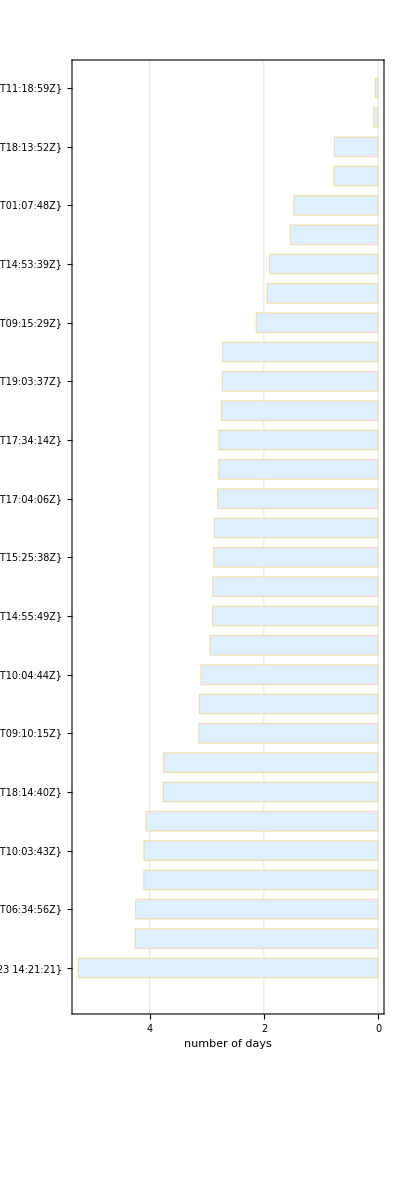

```mathematica
GitHubBarChart["yujieteo","play"]
```